## Computing p(χ_eff = 0) Maria Okounkova

```mathematica
First let's compute p(Subscript[χ, eff]| q, ℳ) = 0
```

#### χ_eff in terms of {q, ℳ}

```mathematica
Solutionm1m2 = Solve[(m1*m2)^(3/5) / (m1 + m2)^(1/5)== ℳ  &&  m1/m2 == q,{m1,m2}]
```

{{m1→q^(2/5) (1+q)^(1/5) ℳ,m2→((1+q)^(1/5) ℳ)/q^(3/5)},{m1→-(-1)^(1/5) q^(2/5) (1+q)^(1/5) ℳ,m2→-((-1)^(1/5) (1+q)^(1/5) ℳ)/q^(3/5)},{m1→(-1)^(2/5) q^(2/5) (1+q)^(1/5) ℳ,m2→((-1)^(2/5) (1+q)^(1/5) ℳ)/q^(3/5)},{m1→-(-1)^(3/5) q^(2/5) (1+q)^(1/5) ℳ,m2→-((-1)^(3/5) (1+q)^(1/5) ℳ)/q^(3/5)},{m1→(-1)^(4/5) q^(2/5) (1+q)^(1/5) ℳ,m2→((-1)^(4/5) (1+q)^(1/5) ℳ)/q^(3/5)}}

```mathematica
Subm1m2 = Solutionm1m2[[1]]
```

{m1→q^(2/5) (1+q)^(1/5) ℳ,m2→((1+q)^(1/5) ℳ)/q^(3/5)}

```mathematica
ChiEffectivem1m2 = (a1 * (Cos[θ1]/m1) + (a2 * Cos[θ2])/m2)/(m1 + m2)
```

((a1 Cos[θ1])/m1+(a2 Cos[θ2])/m2)/(m1+m2)

```mathematica
ChiEffective =ChiEffectivem1m2 /. Subm1m2 // FullSimplify
```

(q^(1/5) (a1 Cos[θ1]+a2 q Cos[θ2]))/((1+q)^(7/5) ℳ^2)

#### Prior distributions

```mathematica
Pa[a_] := 1
Pθ[θ_] := Sin[θ]/2
Pϕ[ϕ_] := 1/(2*Pi)
```

```mathematica
Integrate[Pa[a], {a, 0, 1}]
```

```mathematica
Integrate[Pθ[θ], {θ, 0, Pi}]
```

```mathematica
Integrate[Pϕ[ϕ], {ϕ, 0, 2*Pi}]
```

```mathematica
PriorProduct = Pa[a1]*Pa[a2]*Pθ[θ1]*Pθ[θ2]*Pϕ[ϕ1]*Pϕ[ϕ2]
```

(Sin[θ1] Sin[θ2])/(16 π^2)

#### Conditional probability p(χ_eff = 0 | a_1, a_2, θ_1, θ_2, ϕ_1, ϕ_2, q, ℳ)

```mathematica
PChiEffGivenAllVariables = DiracDelta[ChiEffective]
```

DiracDelta[(q^(1/5) (a1 Cos[θ1]+a2 q Cos[θ2]))/((1+q)^(7/5) ℳ^2)]

Use the identity δ(Ax) = δ(x) / |A| for scalar A 
(see https://en.wikipedia.org/wiki/Dirac_delta_function#Scaling_and_symmetry)

```mathematica
PChiEffGivenAllVariablesRescaled = (1+q)^(7/5) ℳ^2 / q^(1/5) * DiracDelta[(a1 Cos[θ1]+a2 q Cos[θ2])]
```

((1+q)^(7/5) ℳ^2 DiracDelta[a1 Cos[θ1]+a2 q Cos[θ2]])/q^(1/5)

#### Create integrand to compute the probability p(χ_eff = 0| q, ℳ)

```mathematica
Integrand = PChiEffGivenAllVariablesRescaled * PriorProduct
```

((1+q)^(7/5) ℳ^2 DiracDelta[a1 Cos[θ1]+a2 q Cos[θ2]] Sin[θ1] Sin[θ2])/(16 π^2 q^(1/5))

#### Integrate over ϕ_1, ϕ_2

```mathematica
Integrandϕ = Integrate[Integrand, {ϕ1, 0, 2*Pi}, {ϕ2, 0, 2*Pi}]
```

((1+q)^(7/5) ℳ^2 DiracDelta[a1 Cos[θ1]+a2 q Cos[θ2]] Sin[θ1] Sin[θ2])/(4 q^(1/5))

#### Massaging the terms - take what’s not being integrated over outside

```mathematica
Integrandϕθ1 = Integrate[Integrandϕ, {θ1, 0, Pi}]
```

-((1+q)^(7/5) ℳ^2 (HeavisideTheta[-a1+a2 q Cos[θ2]]-HeavisideTheta[a1+a2 q Cos[θ2]]) Sin[θ2])/(4 a1 q^(1/5))

Let’s remove the coefficient in front to simplify things

```mathematica
Coeff = 1/(4 q^(1/5))(1+q)^(7/5) ℳ^2
```

```mathematica
NoCoeffIntegrandϕθ1 = -1/a1(HeavisideTheta[-a1+a2 q Cos[θ2]]-HeavisideTheta[a1+a2 q Cos[θ2]]) Sin[θ2]
```

Let’s split the above result into two parts - one for each Heaviside function

```mathematica
NoCoeffIntegrandϕθ1FirstHalf= -1/a1(HeavisideTheta[-a1+a2 q Cos[θ2]]) Sin[θ2]
```

-(HeavisideTheta[-a1+a2 q Cos[θ2]] Sin[θ2])/a1

```mathematica
NoCoeffIntegrandϕθ1SecondHalf= -1/a1(-HeavisideTheta[a1+a2 q Cos[θ2]]) Sin[θ2]
```

(HeavisideTheta[a1+a2 q Cos[θ2]] Sin[θ2])/a1

Now for the first half, since a1, a2, and q are positive, we get that the Heaviside function evaluates to zero if Cos(theta_2) < 0. This gives no contribution. However, if Cos(theta_2) > 0, the Heaviside function is nonzero IF a1 < a2 q Cos(theta_2). Thus, we can put in 1 for the Heaviside function and set up a triple integral with 0 < theta_2 < Pi/2, 0 < a2 < 1, and epsilon < a1 < a2 q Cos(theta_2)

```mathematica
IntA1 = Assuming[ q > 1 && 0 < θ2 < Pi/2 && a2 > 0&& ϵ > 0&&  ϵ≠a2 q Cos[θ2], {Integrate[-1/a1 Sin[θ2], {a1, ϵ, a2*q*Cos[θ2]}]}]
```

{-Log[(a2 q Cos[θ2])/ϵ] Sin[θ2]}

```mathematica
IntA2 = Assuming[ q > 1 && 0 < θ2 < Pi/2 && ϵ > 0, {Integrate[IntA1, {a2, 0, 1}]}]
```

{{-(-1+Log[(q Cos[θ2])/ϵ]) Sin[θ2]}}

```mathematica
IntA3 = Assuming[ q > 1 && ϵ > 0, {Integrate[IntA2, {θ2, 0, Pi/2}]}]
```

{{{2-Log[q/ϵ]}}}

```mathematica
NoCoeffIntegrandϕθ1FirstHalfIntegrated = IntA3
```

{{{2-Log[q/ϵ]}}}

Now for the second half, we have that the Heaviside function is nonzero if Cos(theta_2) > 0 for all values of a1 and a2. We also have that if Cos(theta_2) < 0, the Heaviside function is nonzero IF a1 > a2 q | Cos(theta_2)|. Let us thus set up integrals in these two domains

```mathematica
IntB1 = Assuming[ 0 < θ2 < Pi/2 && a2 > 0&& 0 < ϵ < 1, {Integrate[1/a1 Sin[θ2], {a1, ϵ, 1}]}]
```

{-Log[ϵ] Sin[θ2]}

```mathematica
IntB2 =  Assuming[ 0 < θ2 < Pi/2 && a2 > 0&& ϵ > 0 && ϵ ≠1, {Integrate[IntB1, {a2, 0, 1}]}]
```

{{-Log[ϵ] Sin[θ2]}}

```mathematica
IntB3 = Assuming[ ϵ > 0, {Integrate[IntB2, {θ2, 0, Pi/2}]}]
```

{{{-Log[ϵ]}}}

```mathematica
IntC1 = Assuming[ q > 1 && Pi/2 < θ2 < Pi && 0 < a2< 1 && 1+a2 q Cos[θ2]≠0, {Integrate[1/a1 Sin[θ2], {a1,  a2*q*Abs[Cos[θ2]], 1}]}]
```

{-Log[-a2 q Cos[θ2]] Sin[θ2]}

```mathematica
IntC2 = Assuming[ q > 1 && Pi/2 < θ2 < Pi, {Integrate[IntC1, {a2, 0, 1}]}]
```

{{-(-1+Log[-q Cos[θ2]]) Sin[θ2]}}

```mathematica
IntC3 = Assuming[ q > 1, {Integrate[IntC2, {θ2, Pi/2, Pi}]}]
```

{{{2-Log[q]}}}

```mathematica
NoCoeffIntegrandϕθ1SecondHalfIntegrated = IntB3 + IntC3
```

{{{2-Log[q]-Log[ϵ]}}}

Now let’s add up the results of the integral

```mathematica
NoCoeffIntegrated = NoCoeffIntegrandϕθ1SecondHalfIntegrated + NoCoeffIntegrandϕθ1FirstHalfIntegrated
```

{{{4-Log[q]-Log[q/ϵ]-Log[ϵ]}}}

```mathematica
NoCoeffIntegrated = Assuming[q > 1 && ϵ > 0, FullSimplify[NoCoeffIntegrated]]
```

{{{4-2 Log[q]}}}

```mathematica
PChieffGivenqℳ = Coeff * NoCoeffIntegrated
```

{{{((1+q)^(7/5) ℳ^2 (4-2 Log[q]))/(4 q^(1/5))}}}

#### Plot the result as a function of q

```mathematica
PChieffGivenqℳ / ℳ^2
```

{{{((1+q)^(7/5) (4-2 Log[q]))/(4 q^(1/5))}}}

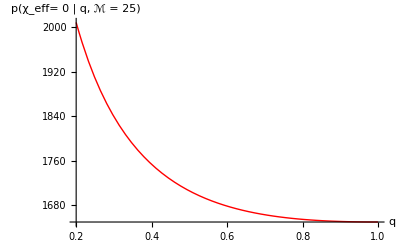

```mathematica
Plot[PChieffGivenqℳ / ℳ^2 * 25^2,{q, 0.2, 1.0}, AxesLabel-> {"q", "p(χ_eff= 0 | q, ℳ = 25)"}, LabelStyle->Directive[Bold, Medium], PlotStyle->{Red, Thick}]
```

```mathematica
Now using priors for q and ℳ, let's compute p(Subscript[χ, eff]) = 0
```

We define q to be uniform in [0.2, 1.0], and ℳ to be uniform in [25, 40]

```mathematica
Pq[q_] := 1/(1 - 0.2)
Pℳ[ℳ_] := 1.0/(40 - 25)
```

```mathematica
Integrate[Pq[q], {q, 0.2, 1}]
Integrate[Pℳ[ℳ], {ℳ, 25, 40}]
```

#### Integrate the p(χ_eff | q, ℳ) result

```mathematica
PChieffGivenq = Integrate[PChieffGivenqℳ, {ℳ, 25, 40}]
```

{{{(16125 (1+q)^(7/5) (4-2 Log[q]))/(4 q^(1/5))}}}

```mathematica
PChieff = Integrate[PChieffGivenq, {q, 0.2, 1}]
```

{{{35480.4}}}